```mathematica
ClearAll;
```

```mathematica
sinc[x_]:=Sinc[π x];
```

```mathematica
lanczos[n_,x_]:=LanczosWindow[x/ (2*n)]sinc[x];
```

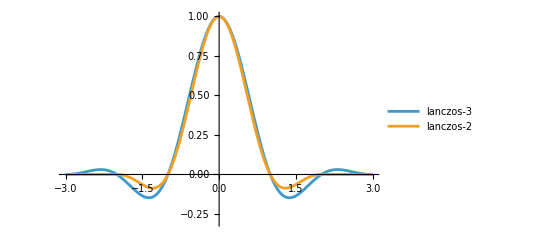

```mathematica
Plot[{lanczos[3,x], lanczos[2, x]}, {x,-3,3}, PlotRange->{-0.3, 1}, PlotLegends->Placed[{"lanczos-3", "lanczos-2"}, {Left, Top}]]
```